```mathematica
ClearAll["Global`*"]
(*wektory przemieszczenia i prędkości mas*)
rm={x[t]+l*Sin[ϕ[t]],y[t]+l*Cos[ϕ[t]]};
rM={x[t],y[t]};
vm=D[rm,t]
vM=D[rM,t];
dlvm=vm.vm;
dlvM=vM.vM;
```

{x'[t]+l Cos[ϕ[t]] ϕ'[t],y'[t]-l Sin[ϕ[t]] ϕ'[t]}

```mathematica
Ekin=1/2*M*dlvM+1/2*m*dlvm;

Epot=-m*g*(y[t]+l*Cos[ϕ[t]])+1/2*k1*((-b-x[t])^2+(y[t])^2)+1/2*k2*((a-x[t])^2+(y[t])^2);
```

```mathematica
(*lagrangian*)
```

```mathematica
L=Ekin-Epot;
Ecal=Ekin+Epot;
```

```mathematica
(*warunki początkowe*)
```

```mathematica
a=1(*m*);
b=1(*m*);
l=1(*m*);
g=981/100(*m/s*);
m=5(*kg*);
M=4(*kg*);
k1=2(*N/m*);
k2=2(*N/m*);
tmax=20(*s*);

(*numeryczne rozwiazanie rownan Lagranga-Eulera*)
num=NDSolve[{D[D[L,x'[t]],t]==D[L,x[t]],D[D[L,y'[t]],t]==D[L,y[t]],D[D[L,ϕ'[t]],t]==D[L,ϕ[t]],x[0]==0(*m*),y[0]==0(*m*),ϕ[0]==(5*π)/3(*rad*),x'[0]==0(*m/s*),y'[0]==0(*m/s*),ϕ'[0]==0(*m=rad/s*)},{x[t],y[t],ϕ[t],x'[t],y'[t],ϕ'[t]},{t,0,tmax}];
```

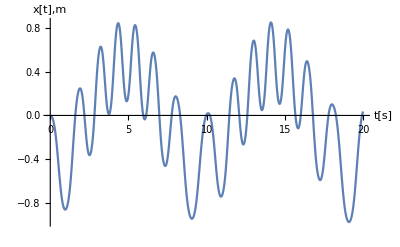

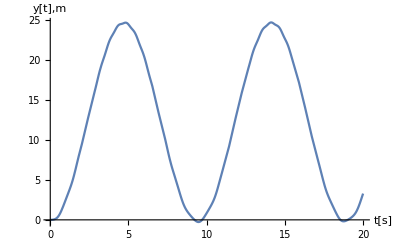

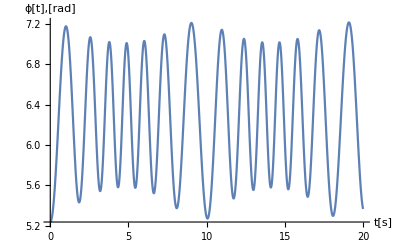

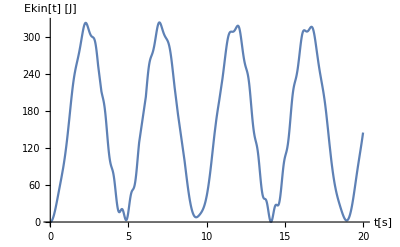

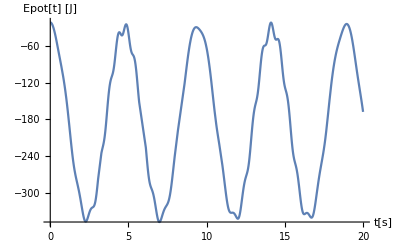

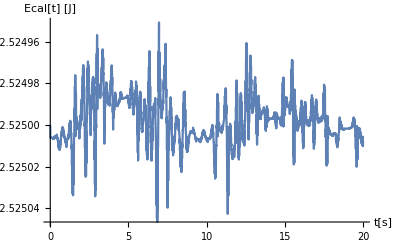

```mathematica
Plot[Evaluate[x[t]/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","x[t],m"}]
Plot[Evaluate[y[t]/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","y[t],m"}]
Plot[Evaluate[ϕ[t]/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","ϕ[t],[rad]"}]
Plot[Evaluate[Ekin/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","Ekin[t] [J]"}]
Plot[Evaluate[Epot/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","Epot[t] [J]"}]
Plot[Evaluate[Ecal/.Flatten[num]],{t,0,tmax},PlotRange->All,AxesLabel->{"t[s]","Ecal[t] [J]"}]
```

```mathematica
Export["C:\\Users\\wiktor\\Desktop\\epot.jpg",%27,"JPEG"]
```

C:\Users\wiktor\Desktop\epot.jpg

```mathematica
Export["C:\\Users\\wiktor\\Desktop\\x[t].jpg",%24,"JPEG"]
```

C:\Users\wiktor\Desktop\x[t].jpg

```mathematica
Export["C:\\Users\\wiktor\\Desktop\\y[t].jpg",%25,"JPEG"]
```

C:\Users\wiktor\Desktop\y[t].jpg

```mathematica
Export["C:\\Users\\wiktor\\Desktop\\kat phi.jpg",%26,"JPEG"]
```

C:\Users\wiktor\Desktop\kat phi.jpg

```mathematica
Export["C:\\Users\\wiktor\\Desktop\\ecal.jpg",%29,"JPEG"]
```

C:\Users\wiktor\Desktop\ecal.jpg

```mathematica
x[t_]:=Evaluate[x[t]/.Flatten[num]];
y[t_]:=Evaluate[y[t]/.Flatten[num]];
ϕ[t_]:=Evaluate[ϕ[t]/.Flatten[num]];




(*kod sprężyny pożyczony z wykładu prof.Golaka*)
gsprezyna1[Pp0_,Pk0_,skala0_]:=Module[{Pp=Pp0,Pk=Pk0,skala=skala0,h,t,a,tab1,d,theta,i,tab5,tab6,Sprezyna6},
h[t_,a_,skala_]:=If[t≥a/18&&t≤17*a/18,skala*Sin[18*Pi/a*(t-a/18)],0];
tab1[a_,skala_]:=Simplify[Table[{t,h[t,a,skala]},{t,0,a,a/36}],a>0];
d[Pp_,Pk_]:=Sqrt[(Pk-Pp).(Pk-Pp)];
theta[Pp_,Pk_]:=ArcTan[Pk[[1]]-Pp[[1]],Pk[[2]]-Pp[[2]]];
tab5[Pp_,Pk_,skala_]:=Table[RotationMatrix[theta[Pp,Pk]].tab1[d[Pp,Pk],skala][[i]],{i,1,37}];
tab6[Pp_,Pk_,skala_]:=Transpose[{Transpose[tab5[Pp,Pk,skala] ][[1]]+Pp[[1]],Transpose[tab5[Pp,Pk,skala]][[2]]+Pp[[2]]}];
Sprezyna6[Pp_,Pk_,skala_]:=Line[tab6[Pp,Pk,skala]];Graphics[Sprezyna6[Pp,Pk,skala]]
]

gsprezyna2[Pp0_,Pk0_,skala0_]:=Module[{Pp=Pp0,Pk=Pk0,skala=skala0,h,t,a,tab1,d,theta,i,tab5,tab6,Sprezyna6},
h[t_,a_,skala_]:=If[t≥a/18&&t≤17*a/18,skala*Sin[18*Pi/a*(t-a/18)],0];
tab1[a_,skala_]:=Simplify[Table[{t,h[t,a,skala]},{t,0,a,a/36}],a>0];
d[Pp_,Pk_]:=Sqrt[(Pk-Pp).(Pk-Pp)];
theta[Pp_,Pk_]:=ArcTan[Pk[[1]]-Pp[[1]],Pk[[2]]-Pp[[2]]];
tab5[Pp_,Pk_,skala_]:=Table[RotationMatrix[theta[Pp,Pk]].tab1[d[Pp,Pk],skala][[i]],{i,1,37}];
tab6[Pp_,Pk_,skala_]:=Transpose[{Transpose[tab5[Pp,Pk,skala] ][[1]]+Pp[[1]],Transpose[tab5[Pp,Pk,skala]][[2]]+Pp[[2]]}];
Sprezyna6[Pp_,Pk_,skala_]:=Line[tab6[Pp,Pk,skala]];Graphics[Sprezyna6[Pp,Pk,skala]]
]
gs1[t_,skala_]:=gsprezyna1[{a,0},{x[t],-y[t]},skala];
gs2[t_,skala_]:=gsprezyna2[{-b,0},{x[t],-y[t]},skala];

wahadlo[t_]=Line[{{x[t],-y[t]},{x[t]+l*Sin[ϕ[t]],-(y[t]+l*Cos[ϕ[t]])}}];
masa1[t_]=Disk[{x[t],-y[t]},1/10];
masa2[t_]=Disk[{x[t]+l*Sin[ϕ[t]],-(y[t]+l*Cos[ϕ[t]])},1/10];

gmasa1[t_]:=Graphics[masa1[t]];
gmasa2[t_]:=Graphics[masa2[t]];
gwahadlo[t_]:=Graphics[wahadlo[t]];
Animate[Show[gs1[t,1/20],gs2[t,1/20],gmasa1[t],gmasa2[t],gwahadlo[t],PlotRange->All],{t,0,tmax}]
```